```mathematica
sf[f_,x_,a_,b_,m_]:=Module[{},
h=(b-a)/(2m)//N;
s=f/.x->a ; 
s=s+2*Sum[f/.x->(a+2i*h),{i,1,m-1}];s=s+4*Sum[f/.x->(a+(2i-1)*h),{i,1,m}];s=s+f/.x->b;
s=h/3*s
]
```

```mathematica
sf[E^(-x^2),x,0,1,5]
```

0.746825

```mathematica
(*..............*)
f[x_]=Cos[5x]-7x+1
```

1-7 x+Cos[5 x]

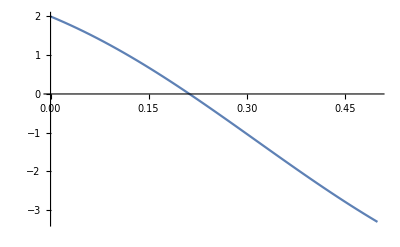

```mathematica
Plot[f[x],{x,0,0.5}]
```

```mathematica
f[0]*f[0.5]<0
```

True

```mathematica
a=0;b=0.5;
```

```mathematica
While[Abs[b-a]>=10^-3 && f[(a+b)/2]!=0,
If[f[a]*f[(a+b)/2]<0,
b=(a+b)/2,
a=(a+b)/2
];
]
```

```mathematica
Print[{a,b}]
```

{0.211914,0.212891}

```mathematica
(*...........*)
```

```mathematica
f[x_]=Cos[5x]-7x+1
```

```mathematica
1-7 x+Cos[5 x]
```

```mathematica
Plot[f[x],{x,0,0.5}]
```

-Graphics-

```mathematica
g[x_]=(Cos[5x]+1)/7
```

1/7 (1+Cos[5 x])

```mathematica
f[0]*f[0.5]<0
```

True

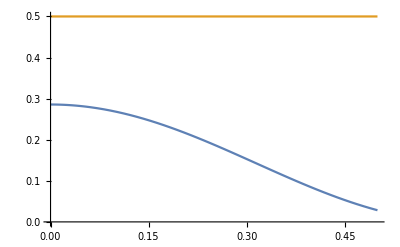

```mathematica
Plot[{g[x],0.5},{x,0,0.5}]
```

```mathematica
(*g:[0,0.5]->[0,0.5]*)
prvi[x_]=D[g[x],x]
```

-5/7 Sin[5 x]

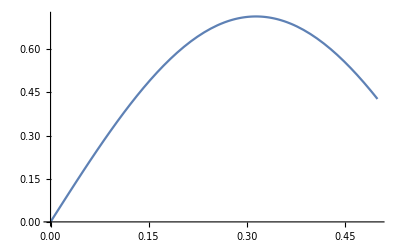

```mathematica
Plot[Abs[prvi[x]],{x,0,0.5}]
```

```mathematica
(*|g'{x}|<1, za xϵ[0,0.5]*)
iter[0]=0//N;
iter[1]=0.5;
i=1;
While[Abs[iter[i]-iter[i-1]]>=10^-4,
iter[i+1]=g[iter[i]];
i=i+1;
]
```

```mathematica
Table[iter[k],{k,0,i}]
```

{0.,0.5,0.0284081,0.284276,0.164123,0.240253,0.194454,0.223346,0.205517,0.216698,0.20975,0.214094,0.211388,0.213077,0.212024,0.212681,0.212271,0.212527,0.212367,0.212467}

```mathematica
(*..........*)
```

```mathematica
njutn[f_,x_,x0_,atol_]:=Module[{},
iter[0]=x0;
izvod=D[f,x];
iter[1]=iter[0]-(f/.x->iter[0])/(izvod/.x->iter[0]);
i=1;
While[Abs[iter[i]-iter[i-1]]>=atol,
iter[i+1]=iter[i]-(f/.x->iter[i])/(izvod/.x->iter[i]);
i=i+1;
];
iter[i]
]
```

```mathematica
f[x_]=Cos[5x]-7x+1;
```

```mathematica
njutn[f[x],x,0.5,10^-4]
```

0.212429